```mathematica
Remove["Global`*"]
(*Constants*)
```

```mathematica
c = 2.99792458*^8;
h = 6.62607004*^-34;
ℏ = h/(2π);
ϵo = 8.8541878128*^-12;
kb = 1.38064852*^-23;
e = 1.60217662*^-19;
a0 = 0.529177210903*^-10;
```

```mathematica
(*The experimental procedure for our CaO^+ rotational spectroscopy experiment will look something like the following:

1)Load a bi-sample of Ca^+ and CaO^+into the ion trap. The Ba^+is laser cooled and acts as a sympathetic coolant for the BaCl^+molecules. We are interested in driving a rotationally-state selective two-photon dissociation transition in BaCl^+that can be used to infer internal state populations
   2)Introduce both an IR beam for driving a v->v' overtone transitions and also a 266 nm photodissociating beam (PD beam) that will drive the v'->dissociaiton transition
     3) As a detection of this dissociation event, we will monitor the amount of Ba^+ions in our trap since the dissociated BaCl^+molecules will turn into Ba^+ions that can be laser-cooled. Also we can look for BaCl^+decay in the ToF-MS


We thus want to cosntruct a compuational model for the experiment that can predict the amount of Ba and BaCl^+ion our system for different types of overtone transitions, diss energies, etc. We also want a realistic picture of what our controls with no IR beam will look like comparatively*)  



(*First upload the cross section for each vibrational state from a set of BCONT output files. For some reason there is an error in the BCONT output files when calculating the red side of the PD cross section for the v>6, but this shouldnt hurt us too mcuh for now*)
```

```mathematica
(*Make the matrixes for the various transition Properties*)
m = (40 16)/(40 + 16) 1.67*^-27; (*reduced mass of the^40 Ca^+ +^16 O system in kg*)
vMax=4; (*maximum number of vibrational levels to include in the model*)
jMax=70; (*maximum number of rotational levels (per vibrational manifold) to include in the model*)
DCM=3.335×10^-30; (*conversion factor to convert dipole matrix elements calculated from LEVEL into SI units*)

SetDirectory["C:\\Users\\haowu\\OneDrive\\Documents\\MOTION\\REMPD\\level"]
(*import LEVEL data file*)
baseD=Drop[Import[FileNames["fort.8"][[1]],"Table"],11];
```

C:\Users\haowu\OneDrive\Documents\MOTION\REMPD\level

```mathematica
(*extract the transition energy and einstein a coefficients for every ro-vibrational transition in the molecules and store them into matrices*)


rotDown=Quiet[Flatten[ToExpression[StringTrim[#,{"(",")"}]&/@baseD[[;;,{2}]]]]]; (*label of lower rotational state*)
vUp=baseD[[;;,3]] (*label of upper vibrational state*);
vDown=baseD[[;;,5]](* "" "" "" lower vib. state*);
dm=baseD[[;;,-1]] (*dipole moment between states*);
enDiff=Abs[baseD[[;;,-4]]] (*en. diff between states*);
Acoe=baseD[[;;,-3]] ;
rotUp=rotDown 0;

Do[
rotUp[[i]]=Piecewise[{{rotDown[[i]]+1,baseD[[i]][[1]]=="R("},
							{rotDown[[i]]-1,baseD[[i]][[1]]=="P("},
							{rotDown[[i]],baseD[[i]][[1]]=="Q("}
							}],{i,1,rotDown//Length}] ;

(*label of upper rotational states*)
```

```mathematica
master=Transpose[{rotDown,rotUp,vDown,vUp,dm,enDiff,Acoe}]; (*master array of all transitions and their properties*)
```

```mathematica
DMmasterUP=Gather[#,#1[[1]]==#2[[1]] &]&/@Gather[Select[master,#[[1]]<jMax  &&  #[[2]]<jMax && #[[3]]<vMax && #[[4]]<vMax &],#1[[3]]==#2[[3]] &]; (*these arrays contain all transition that start from a particular transition and go upward, useful for stimulated absorption*)
EnmasterUP= Gather[#,#1[[1]]==#2[[1]]&]&/@Gather[Select[master,#[[1]]<jMax  && #[[2]]<jMax && #[[3]]<vMax && #[[4]]<vMax &],#1[[3]]==#2[[3]] &];
DMslimUP=DCM Table[Table[If[i==vMax && j==jMax,{0},DMmasterUP[[i]][[j]][[;;,5]]],{j,1,jMax}],{i,1,vMax}];
enSlimUP=2 π 100 c Quiet[ Table[Table[If[i==vMax && j==jMax,{1*^-10},EnmasterUP[[i]][[j]][[;;,6]]],{j,1,jMax}],{i,1,vMax}]];
HonlUP=Table[Table[Table[If[i==vMax && j==jMax+1,{0},If [EnmasterUP[[i]][[j]][[;;,2]][[k]]>EnmasterUP[[i]][[j]][[;;,1]][[k]],(EnmasterUP[[i]][[j]][[;;,1]][[k]]+1)/(2EnmasterUP[[i]][[j]][[;;,2]][[k]]+1),EnmasterUP[[i]][[j]][[;;,1]][[k]]/(2EnmasterUP[[i]][[j]][[;;,2]][[k]]+1)]],{k,1,EnmasterUP[[i]][[j]][[;;,1]]//Length,1}],{j,1,jMax}],{i,1,vMax}];
HonlUP[[vMax]][[jMax]]={0};
AmasterUP=Abs[2/3 1/(ϵo h c^3)(enSlimUP)^3(DMslimUP)^2 HonlUP];
BcoeUP=Table[Table[Table[(2EnmasterUP[[i]][[j]][[;;,2]][[k]]+1)/(2EnmasterUP[[i]][[j]][[;;,1]][[k]]+1),{k,1,EnmasterUP[[i]][[j]][[;;,1]]//Length,1}],{j,1,jMax}],{i,1,vMax}];
BcoeUP[[vMax]][[jMax]]={0};

AcoeUP= Table[Table[DMmasterUP[[i]][[j]][[;;,7]],{j,1,jMax}],{i,1,vMax}];
Babsorp=Abs[1/8 c^2/(π h)((enSlimUP+3.335×10^-30)/(2 π)  )^-3*AcoeUP*BcoeUP];
Babsorpe=Abs[1/8 c^2/(π h)((enSlimUP+3.335×10^-30)/(2 π))^-3*AcoeUP];
```

```mathematica
(*these arrays contain all transition that start from a particular transition and go downward, useful for stimulated emission and spontaneous emission*)
DMmasterDOWN=Gather[#,#1[[2]]==#2[[2]] &]&/@Gather[Select[master,#[[1]]<jMax   && #[[3]]≤ vMax && #[[4]]≤ vMax &],#1[[4]]==#2[[4]] &];
EnmasterDOWN= Gather[#,#1[[2]]==#2[[2]]&]&/@Gather[Select[master,#[[1]]<jMax    && #[[3]]≤ vMax && #[[4]]≤ vMax &],#1[[4]]==#2[[4]] &];
DMmasterDOWN[[1]]=Prepend[DMmasterDOWN[[1]],{{0,0,0,0,0,0,0}}];
EnmasterDOWN[[1]]=Prepend[EnmasterDOWN[[1]],{{0,0,0,0,0,.1,0}}];
DMslimDOWN=DCM Table[Table[DMmasterDOWN[[i]][[j]][[;;,5]],{j,1,jMax}],{i,1,vMax}];
enSlimDOWN=Table[Table[ 2 π 100  c EnmasterDOWN[[i]][[j]][[;;,6]],{j,1,jMax}],{i,1,vMax}];


JDOWN=Table[Table[DMmasterDOWN[[i]][[j]][[;;,1]],{j,1,jMax}],{i,1,vMax}];
Jup=Table[Table[EnmasterDOWN[[i]][[j]][[;;,2]],{j,1,jMax}],{i,1,vMax}];
HonlDOWN=Table[Table[Table[If [EnmasterDOWN[[i]][[j]][[;;,2]][[k]]>EnmasterDOWN[[i]][[j]][[;;,1]][[k]],(EnmasterDOWN[[i]][[j]][[;;,1]][[k]]+1)/(2EnmasterDOWN[[i]][[j]][[;;,2]][[k]]+1),EnmasterDOWN[[i]][[j]][[;;,1]][[k]]/(2EnmasterDOWN[[i]][[j]][[;;,2]][[k]]+1)],{k,1,EnmasterDOWN[[i]][[j]][[;;,1]]//Length,1}],{j,1,jMax}],{i,1,vMax}];

BcoeDOWN=Table[Table[Table[(2EnmasterDOWN[[i]][[j]][[;;,2]][[k]]+1)/(2EnmasterDOWN[[i]][[j]][[;;,1]][[k]]+1),{k,1,EnmasterDOWN[[i]][[j]][[;;,1]]//Length,1}],{j,1,jMax}],{i,1,vMax}];
AmasterDOWN=Abs[2/3 1/(ϵo h c^3)(enSlimDOWN)^3(DMslimDOWN)^2*HonlDOWN];

AcoeDOWN= Table[Table[DMmasterDOWN[[i]][[j]][[;;,7]],{j,1,jMax}],{i,1,vMax}];
```

```mathematica
(*absorption coefficient*)
```

```mathematica
Bemission=Abs[1/8 c^2/(π h)((enSlimDOWN+3.335×10^-30)/(2 π) )^-3*AcoeDOWN];
Bemmsiona=Abs[1/8 c^2/(π h)((enSlimDOWN+3.335×10^-30)/(2 π))^-3*AcoeDOWN*BcoeDOWN];
```

```mathematica
Be=.37 h 100 c;
ωe=634*100 c 2 π;
vibMaxBoltz[v_,T_]:=(Exp[-ℏ ωe/(2kb T)](1-Exp[-ℏ ωe/(kb T)])^-1)^-1 Exp[-ℏ (ωe(v+1/2))/(kb T)]
MaxBoltz[v_,J_,T_]:=vibMaxBoltz[v,T]((2J+1)Exp[-(Be J(J+1))/(kb T)])/Sum[(2k+1)Exp[-(Be k(k+1))/(kb T)],{k,0,300}]

(*for comparison of Max-Boltz vibrational populations with model, sum over rotational levels*)
```

```mathematica
T=4; (*internal temp of CaO^+sample in Kelvin*)
(*set of master equations including just BBR*)
masterEqns=Table[Table[Subscript[n, i,j]'[t]== -Total[AcoeDOWN[[i+1]][[j+1]]]Subscript[n, i,j][t](*spon emission out*)

+If[i==vMax-1 && j==jMax-1,0,Sum[AcoeUP[[i+1,j+1]][[k]]Subscript[n, DMmasterUP[[i+1,j+1]][[k]][[4]],DMmasterUP[[i+1,j+1]][[k]][[2]]][t],{k,1,AcoeUP[[i+1]][[j+1]]//Length}]](*spon emission in*)

+If[i==vMax-1 && j==jMax-1,0,Sum[Abs[8π h((enSlimUP[[i+1,j+1]][[k]])/(2 π))^3]/(c^2(Exp[(ℏ enSlimUP[[i+1,j+1]][[k]])/(kb T)]-1-3.335×10^-30))Babsorpe[[i+1,j+1]][[k]]Subscript[n, DMmasterUP[[i+1,j+1]][[k]][[4]],DMmasterUP[[i+1,j+1]][[k]][[2]]][t],{k,1,DMmasterUP[[i+1]][[j+1]]//Length}]]+If[i==vMax-1 && j==jMax-1,0,Sum[Abs[8π h((enSlimUP[[i+1,j+1]][[k]])/(2 π))^3]/(c^2(Exp[(ℏ enSlimUP[[i+1,j+1]][[k]])/(kb T)]-1-3.335×10^-30))(-Babsorp[[i+1,j+1]][[k]]Subscript[n, i,j][t]),{k,1,Babsorp[[i+1]][[j+1]]//Length}]]

(*BBR stimulated absorption*)
+Sum[Abs[8π h((enSlimDOWN[[i+1,j+1]][[k]])/(2 π))^3]/(c^2(Exp[(ℏ enSlimDOWN[[i+1,j+1]][[k]])/(kb T)]-1-3.335×10^-30))(-Bemission[[i+1,j+1]][[k]]Subscript[n, i,j][t])
(*BBR stimulated emission*)

,{k,1,Bemission[[i+1]][[j+1]]//Length}]+Sum[Abs[8π h((enSlimDOWN[[i+1,j+1]][[k]])/(2 π))^3]/(c^2(Exp[(ℏ enSlimDOWN[[i+1,j+1]][[k]])/(kb T)]-1-3.335×10^-30))(Bemmsiona[[i+1,j+1]][[k]]Subscript[n, DMmasterDOWN[[i+1,j+1]][[k]][[3]],DMmasterDOWN[[i+1,j+1]][[k]][[1]]][t])
(*BBR stimulated emission*)

,{k,1,DMmasterDOWN[[i+1]][[j+1]]//Length}]
,{i,0,vMax-1}],{j,0,jMax-1}];
```

General::munfl: 1/(1.70004×10^308) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(*here I set the initial conditions to be perverse, all the pop starts in the highest state*)
initialCon={};

Do[Do[AppendTo[initialCon
,Subscript[n, i,j][0]==0],{i,0,vMax-1}],{j,0,jMax-1}];
initialCon[[9]]=(Subscript[n, 0,2][0]== 1);


eqnSolve={};

(*Do[Do[AppendTo[initialCon
,Subscript[n, i,j][0]==MaxBoltz[i,j,300]],{i,0,vMax-1}],{j,0,jMax-1}];*)
(*array containing all depedent variables*)
Do[Do[AppendTo[eqnSolve
,Subscript[n, i,j][t]],{i,0,vMax-1}],{j,0,jMax-1}];
totalEqns={};
Do[Do[AppendTo[totalEqns
,masterEqns[[i]][[j]]],{i,1,jMax}],{j,1,vMax}];
```

```mathematica
Flatten[masterEqns]//Length
eqnSolve//Length
initialCon//Length
```

280

280

280

```mathematica
sln=NDSolve[Join[totalEqns,initialCon],Reverse[eqnSolve],{t,0,40000},Method->{"EquationSimplification"->"Residual"}];
```

General::munfl: 9.13669×10^-100 4.40109×10^-211 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.13669×10^-100 3.97387×10^-218 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.13669×10^-100 2.74887×10^-225 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

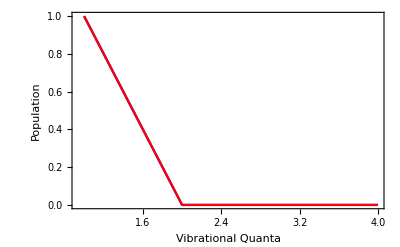

General::munfl: Exp[-718.935] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-738.632] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-758.595] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

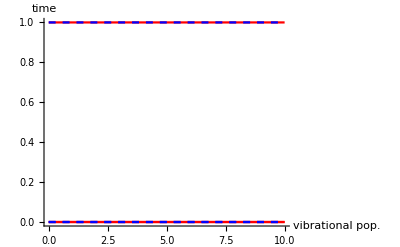

```mathematica
(*to make sure i didn't mess up, let's compare to a Maxwell Boltzmann distribution to if they have agreement*)

vibLevel=0;
vib1[t_]=Total[Table[Sum[Subscript[n, i,j][t]/.sln,{j,0,jMax-1}],{i,vibLevel,vibLevel}]];
vibLevel=1;
vib2[t_]=Total[Table[Sum[Subscript[n, i,j][t]/.sln,{j,0,jMax-1}],{i,vibLevel,vibLevel}]];
vibLevel=2;
vib3[t_]=Total[Table[Sum[Subscript[n, i,j][t]/.sln,{j,0,jMax-1}],{i,vibLevel,vibLevel}]];
MBVib=Table[Sum[MaxBoltz[i,k,T],{k,0,jMax-1}],{i,0,vMax-1}];

tProbe=5;

(*this plots the expected vibrational populations for both the model and Max-Boltz predicitons at a time tProbe*)
Show[ListLinePlot[MBVib,PlotRange->All,PlotStyle->Blue,Frame->True,FrameLabel->{"Vibrational Quanta","Population"}],ListLinePlot[Flatten[Table[Sum[Subscript[n, i,j][t]/.sln,{j,0,jMax-1}]/.t->tProbe,{i,0,vMax-1}]],PlotStyle->Red,PlotRange->All]]

(*this plots the expected vibrational populations for both the model and Max-Boltz predicitons at a time tProbe*)
Show[Plot[{vib1[t],vib2[t],vib3[t]},{t,0,10},PlotRange->All,PlotStyle->Red,AxesLabel->{"vibrational pop.","time"}],Plot[{Sum[MaxBoltz[0,k,T],{k,0,100}],Sum[MaxBoltz[2,k,T],{k,0,100}],Sum[MaxBoltz[1,k,T],{k,0,100}]},{t,0,10},PlotStyle->Table[{Blue,Dashed},{i,1,3}]]]

(*looks pretty good*)
```

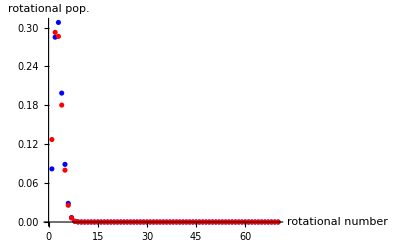

```mathematica
(*Now let's look at rotational level populations*)
tProbe=40000;
rotationalPop=Flatten[Table[Subscript[n, 0,J][t]/.sln/.t->tProbe,{J,0,jMax-1}]];
MBrotPop=Table[MaxBoltz[0,J,T],{J,0,jMax-1}];
ListPlot[{rotationalPop,MBrotPop},AxesLabel->{"rotational number","rotational pop."},PlotStyle->{Blue,{Red,Dashed}},PlotRange->All]

(*okay, it looks in model the molecules aren't equillibrated rotationally, even at 10000 sec. Blackbody spectrum isn't peaked very strongly in the microwave regime so this isn't surprising. But the lack of equillibriation is also partly because I started with crazy initial conditions. If I make it more reasonable, the boltzman distribution should be fine, or I could just wait longer for the populations to redistribute. But I can't propogate my rate equation model past 10000 sec without crashing my computer so I'm going to leave it for now*)
```

```mathematica
Nn[t_]=Subscript[n, 0,2][t]/.sln;
Nn[000]
```

{1.}

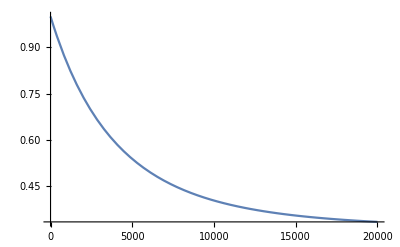

```mathematica
Plot[Nn[t],{t,0,20000}]
```